# Practica 2: Sistemas de ecuaciones diferenciales

## Sistemas de ecuaciones diferenciales

### Sistemas de ecuaciones diferenciales no homogéneos con coeficientes constantes

De cada uno de los siguientes sistemas de ecuaciones diferenciales obtenga:

a) Los valores de estado estacionario.
b) El análisis de estabilidad.
c) El diagrama de fases.

1.	ẋ=-2x+y+3
	ẏ=  x-2y+3

a) Valores de estado estacionario

```mathematica
<<VectorFieldPlots`
```

General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
A1={{-2,1},{1,-2}};MatrixForm[A1](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-2 | 1
1 | -2)

```mathematica
b1={{3},{3}};MatrixForm[b1](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(3
3)

```mathematica
MatrixForm[LinearSolve[-A1,b1]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(3
3)

b) Análisis de estabilidad

```mathematica
traA1=Tr[A1](*Traza de la matriz A*)
```

-4

```mathematica
detA1=Det[A1](*Determinante de la matriz A*)
```

3

```mathematica
(traA1)^2-4detA1(* (TrazaA)^2-4det|A| *)
```

4

```mathematica
ec1=CharacteristicPolynomial[A1,λ] (* Polinomio caracteristico de la matriz A *)
```

3+4 λ+λ^2

```mathematica
Solve[ec1==0,λ](* Obteniendo los valores propios *)
```

{{λ→-3},{λ→-1}}

c) Diagrama de fases

```mathematica
eq1={x'[t]==-2x[t]+y[t]+3,y'[t]==x[t]-2y[t]+3};
```

```mathematica
var1={x[t],y[t]};
```

```mathematica
sol1=DSolve[eq1,var1,t];
```

```mathematica
p1=ContourPlot[{-2x+y+3==0,x-2y+3==0},{x,1,5},{y,1,5},Axes->True,Frame->False];
```

```mathematica
p2=VectorFieldPlot[{-2x+y+3,x-2y+3},{x,1,5},{y,1,5},ScaleFunction->(1 &),AspectRatio->1];
```

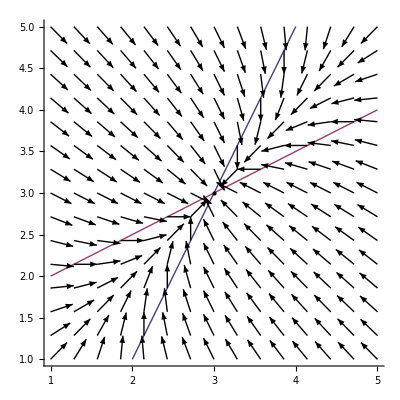

```mathematica
Show[p1,p2]
```

```mathematica
Clear[A1,b1,ec1,eq1,var1,sol1,p1,p2]
```

2.	ẋ=4x- y
	ẏ=2x+y-6

a) Valores de estado estacionario

```mathematica
A2={{4,-1},{2,1}};MatrixForm[A2](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(4 | -1
2 | 1)

```mathematica
b2={{0},{-6}};MatrixForm[b2](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(0
-6)

```mathematica
MatrixForm[LinearSolve[-A2,b2]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(1
4)

b) Análisis de estabilidad

```mathematica
traA2=Tr[A2](*Traza de la matriz A*)
```

5

```mathematica
detA2=Det[A2](*Determinante de la matriz A*)
```

6

```mathematica
(traA2)^2-4detA2(* (TrazaA)^2-4det|A| *)
```

1

```mathematica
ec2=CharacteristicPolynomial[A2,λ] (* Polinomio caracteristico de la matriz A *)
```

6-5 λ+λ^2

```mathematica
Solve[ec2==0,λ](* Obteniendo los valores propios *)
```

{{λ→2},{λ→3}}

c) Diagrama de fases

```mathematica
eq2={x'[t]==4x[t]-y[t],y'[t]==2x[t]+y[t]-6};
```

```mathematica
var2={x[t],y[t]};
```

```mathematica
sol2=DSolve[eq2,var2,t];
```

```mathematica
p3=ContourPlot[{4x-y==0,2x+y-6==0},{x,0,2},{y,2,6},Axes->True,Frame->False];
```

```mathematica
p4=VectorFieldPlot[{4x-y,2x+y-6},{x,0,2},{y,2,6},ScaleFunction->(1 &),AspectRatio->1];
```

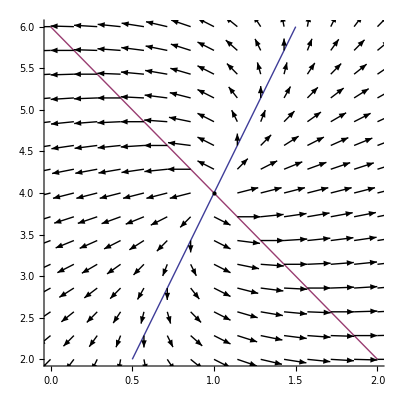

```mathematica
Show[p3,p4]
```

```mathematica
Clear[A2,b2,ec2,eq2,var2,sol2,p3,p4]
```

3.	ẋ= x+2y-6
	ẏ=2x+ y-6

a) Valores de estado estacionario

```mathematica
A3={{1,2},{2,1}};MatrixForm[A3](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(1 | 2
2 | 1)

```mathematica
b3={{-6},{-6}};MatrixForm[b3](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-6
-6)

```mathematica
MatrixForm[LinearSolve[-A3,b3]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(2
2)

b) Análisis de estabilidad

```mathematica
traA3=Tr[A3](*Traza de la matriz A*)
```

2

```mathematica
detA3=Det[A3](*Determinante de la matriz A*)
```

-3

```mathematica
(traA3)^2-4detA3(* (TrazaA)^2-4det|A| *)
```

16

```mathematica
ec3=CharacteristicPolynomial[A3,λ] (* Polinomio caracteristico de la matriz A *)
```

-3-2 λ+λ^2

```mathematica
Solve[ec3==0,λ](* Obteniendo los valores propios *)
```

{{λ→-1},{λ→3}}

c) Diagrama de fases

```mathematica
eq3={x'[t]==x[t]+2y[t]-6,y'[t]==2x[t]+y[t]-6};
```

```mathematica
var3={x[t],y[t]};
```

```mathematica
sol3=DSolve[eq3,var3,t];
```

```mathematica
p5=ContourPlot[{x+2y-6==0,2x+y-6==0},{x,0,4},{y,0,4},Axes->True,Frame->False];
```

```mathematica
p6=VectorFieldPlot[{x+2y-6,2x+y-6},{x,0,4},{y,0,4},ScaleFunction->(1 &),AspectRatio->1];
```

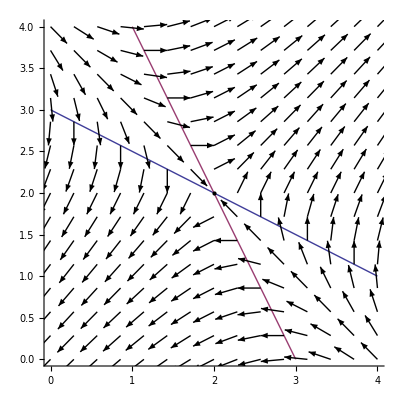

```mathematica
Show[p5,p6]
```

```mathematica
Clear[A3,b3,ec3,eq3,var3,sol3,p5,p6]
```

4.	ẋ=-3x+4y-16	c.i. 	x(0)=2
	ẏ=-2x+  y+1		y(0)=3

```mathematica
A4={{-3,4},{-2,1}};MatrixForm[A4](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-3 | 4
-2 | 1)

```mathematica
b4={{-16},{1}};MatrixForm[b4](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-16
1)

```mathematica
MatrixForm[LinearSolve[-A4,b4]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(4.
7.)

b) Análisis de estabilidad

```mathematica
traA4=Tr[A4](*Traza de la matriz A*)
```

-2

```mathematica
detA4=Det[A4](*Determinante de la matriz A*)
```

5

```mathematica
(traA4)^2-4detA4(* (TrazaA)^2-4det|A| *)
```

-16

```mathematica
ec4=CharacteristicPolynomial[A4,λ] (* Polinomio caracteristico de la matriz A *)
```

5+2 λ+λ^2

```mathematica
Solve[ec4==0,λ](* Obteniendo los valores propios *)
```

{{λ→-1-2 ⅈ},{λ→-1+2 ⅈ}}

c) Diagrama de fases

```mathematica
eq4={x'[t]==-3x[t]+4y[t]-16,y'[t]==-2x[t]+y[t]+1,x[0]==4,y[0]==4};
```

```mathematica
var4={x[t],y[t]};
```

```mathematica
sol4=DSolve[eq4,var4,t];
```

```mathematica
p7=ContourPlot[{-3x+4y-16==0,-2x+y+1==0},{x,0,6},{y,2,9},Axes->True,Frame->False];
```

```mathematica
p8=VectorFieldPlot[{-3x+4y-16,-2x+y+1},{x,0,6},{y,2,9},ScaleFunction->(1 &),AspectRatio->1];
```

```mathematica
p9=ParametricPlot[Evaluate[var4/.sol4],{t,0,7},PlotStyle->{Thickness[0.009],RGBColor[0,0,1]}];
```

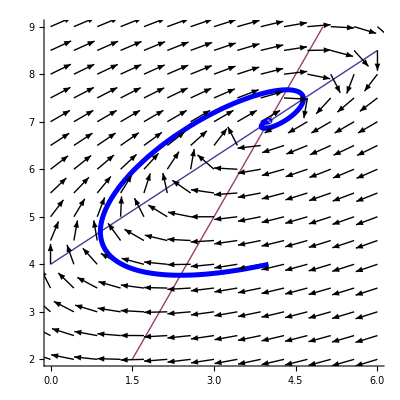

```mathematica
Show[p7,p8,p9]
```

```mathematica
Clear[A4,b4,ec4,eq4,var4,sol4,p7,p8,p9]
```

5.	ẋ=   x+4y-10	c.i. 	x(0)= 2
	ẏ=-4x+ y+ 6		y(0)= 1

```mathematica
A5={{1,4},{-4,1}};MatrixForm[A5](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(1 | 4
-4 | 1)

```mathematica
b5={{-10},{6}};MatrixForm[b5](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-10
6)

```mathematica
MatrixForm[LinearSolve[-A5,b5]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(2
2)

b) Análisis de estabilidad

```mathematica
traA5=Tr[A5](*Traza de la matriz A*)
```

2

```mathematica
detA5=Det[A5](*Determinante de la matriz A*)
```

17

```mathematica
(traA5)^2-4detA5(* (TrazaA)^2-4det|A| *)
```

-64

```mathematica
ec5=CharacteristicPolynomial[A5,λ] (* Polinomio caracteristico de la matriz A *)
```

17-2 λ+λ^2

```mathematica
Solve[ec5==0,λ](* Obteniendo los valores propios *)
```

{{λ→1-4 ⅈ},{λ→1+4 ⅈ}}

c) Diagrama de fases

```mathematica
eq5={x'[t]==x[t]+4y[t]-10,y'[t]==-4x[t]+y[t]+6,x[0]==2,y[0]==1};
```

```mathematica
var5={x[t],y[t]};
```

```mathematica
sol5=DSolve[eq5,var5,t];
```

```mathematica
p10=ContourPlot[{x+4y-10==0,-4x+y+6==0},{x,0,4},{y,0,4.2},Axes->True,Frame->False];
```

```mathematica
p11=VectorFieldPlot[{x+4y-10,-4x+y+6},{x,0,4},{y,0,4.2},ScaleFunction->(1 &),AspectRatio->1];
```

```mathematica
p12=ParametricPlot[Evaluate[var5/.sol5],{t,0,7},PlotStyle->{Thickness[0.009],RGBColor[0,0,1]}];
```

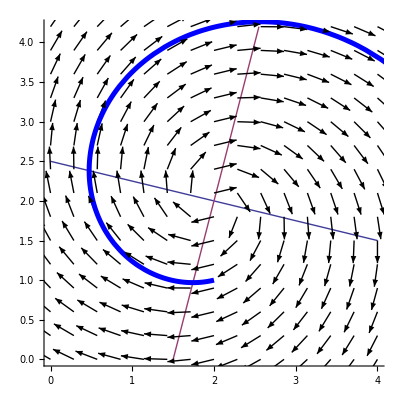

```mathematica
Show[p10,p11,p12]
```

```mathematica
Clear[A5,b5,ec5,eq5,var5,sol5,p10,p11,p12]
```

6.	ẋ= 2x+8y-24	c.i. 	x(0)= 3
	ẏ= -x -2y+  8		y(0)= 2

```mathematica
A6={{2,8},{-1,-2}};MatrixForm[A6](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(2 | 8
-1 | -2)

```mathematica
b6={{-24},{8}};MatrixForm[b6](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-24
8)

```mathematica
MatrixForm[LinearSolve[-A6,b6]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(4
2)

b) Análisis de estabilidad

```mathematica
traA6=Tr[A6](*Traza de la matriz A*)
```

0

```mathematica
detA6=Det[A6](*Determinante de la matriz A*)
```

4

```mathematica
(traA6)^2-4detA6(* (TrazaA)^2-4det|A| *)
```

-16

```mathematica
ec6=CharacteristicPolynomial[A6,λ] (* Polinomio caracteristico de la matriz A *)
```

4+λ^2

```mathematica
Solve[ec6==0,λ](* Obteniendo los valores propios *)
```

{{λ→-2 ⅈ},{λ→2 ⅈ}}

c) Diagrama de fases

```mathematica
eq6={x'[t]==2x[t]+8y[t]-24,y'[t]==-x[t]-2y[t]+8,x[0]==3,y[0]==2};
```

```mathematica
var6={x[t],y[t]};
```

```mathematica
sol6=DSolve[eq6,var6,t];
```

```mathematica
p13=ContourPlot[{2x+8y-24==0,-x-2y+8==0},{x,2,6},{y,1,3},Axes->True,Frame->False];
```

```mathematica
p14=VectorFieldPlot[{2x+8y-24,-x-2y+8},{x,2,6},{y,1,3},ScaleFunction->(1 &),AspectRatio->1];
```

```mathematica
p15=ParametricPlot[Evaluate[var6/.sol6],{t,0,5},PlotStyle->{Thickness[0.009],RGBColor[0,0,1]}];
```

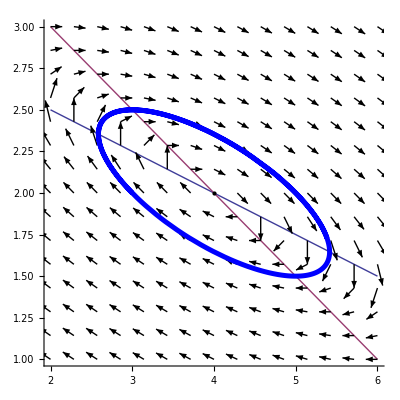

```mathematica
Show[p13,p14,p15]
```

```mathematica
Clear[A6,b6,ec6,eq6,var6,sol6,p13,p14,p15]
```